# Online simulation

## Functions

Sensors are replaced with a function to check if any block causes a collision with the robot’s current position

```mathematica
updateSensors[currentPosition_List, map_List]:=
Block[
{collisions,sensorState},

collisions={
MemberQ[map,{currentPosition[[1]],currentPosition[[2]]+1}],
MemberQ[map,{currentPosition[[1]]+1,currentPosition[[2]]}],
MemberQ[map,{currentPosition[[1]],currentPosition[[2]]-1}],
MemberQ[map,{currentPosition[[1]]-1,currentPosition[[2]]}]};

sensorState=Table[If[collisions[[i]]==True,1,0],{i,Length[collisions]}];
sensorState
]
```

```mathematica
getTimeDifference[tNow_,tBefore_]:=Module[{},Round[QuantityMagnitude[UnitConvert[tNow-tBefore,"Seconds"]]]]
```

```mathematica
updatePosition[currentTime_,statusOld_List,speed_List]:=Module[{newPosition,Δt=getTimeDifference[currentTime,statusOld[[1]]]},
newPosition=Piecewise[{{Round[statusOld[[2]]+{0,Δt}*speed], statusOld[[3]]=="Forward"}, {Round[statusOld[[2]]-{0,Δt}*speed], statusOld[[3]]=="Back"}, {Round[statusOld[[2]]-{Δt,0}*speed], statusOld[[3]]=="Left"}, {Round[statusOld[[2]]+{Δt,0}*speed], statusOld[[3]]=="Right"}, {statusOld[[2]], statusOld[[3]]=="Stop"}}]
]
```

```mathematica
updateWalls2[location_,statusOld_List,sensorsNow_List]:=
Module[
{x=location[[1]],y=location[[2]],newWalls,blockPerimeter},

blockPerimeter=sensorsNow*{{x,y+1},{x+1,y},{x,y-1},{x-1,y}};

blockPerimeter=DeleteCases[blockPerimeter,{0,0}];

newWalls=Join[statusOld[[5]],blockPerimeter];

If[Length[newWalls]>1,newWalls=DeleteCases[newWalls,{}],Nothing];

newWalls
]
```

```mathematica
updateMap[location_List,currentTime_,statusOld_List]:=Module[
{newMap=statusOld[[6]],mapSurface,Δt=getTimeDifference[currentTime,statusOld[[1]]]},
mapSurface=Piecewise[{{Table[{location[[1]],statusOld[[2,2]]+i},{i,Δt}], statusOld[[3]]=="Forward"}, {Table[{location[[1]],statusOld[[2,2]]-i},{i,Δt}], statusOld[[3]]=="Back"}, {Table[{statusOld[[2,1]]+i,location[[2]]},{i,Δt}], statusOld[[3]]=="Right"}, {Table[{statusOld[[2,1]]-i,location[[2]]},{i,Δt}], statusOld[[3]]=="Left"}, {{statusOld[[2]]}, statusOld[[3]]=="Stop"}}];
If[statusOld[[3]]!="Stop",newMap=Join[newMap,mapSurface]];
newMap
]
```

```mathematica
updateDirection2[dirs_List,buttons_List,current_String]:=
Module[
{i,obstacles,placeholder,placeholder2,nextdir,placeholder3},

obstacles=Table[1-buttons[[i]],{i,Length[buttons]}];
placeholder3=DeleteCases[dirs,"Stop"];
placeholder2=DeleteCases[placeholder3*obstacles,0];

If[MemberQ[placeholder3*obstacles,current],nextdir=current,nextdir=RandomChoice[placeholder2]]
]
```

```mathematica
updateDirection3[dirs_List,sensor_List,currentState_String,prevState_List]:=
Module[
{i,obstacles,possibleDirections,nextdir,existingDirections},

obstacles=Table[1-sensor[[i]],{i,Length[sensor]}];
existingDirections=DeleteCases[dirs,"Stop"];
possibleDirections=DeleteCases[existingDirections*obstacles,0];

If[MemberQ[possibleDirections*obstacles,currentState],nextdir=currentState,nextdir=RandomChoice[possibleDirections]]

]
```

## Initialization data

### Map

A full map has to be created in order to allow the rest of the program to function. Thus, the robot explores this virtual environment, only updating its internal lists of collisions and positions without considering the map data.

#### Test 1

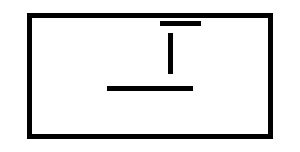

```mathematica
a=Table[{5,i},{i,10}];
b=Table[{i+2,13},{i,10}];
c=Table[{i,-3},{i,-10,10,1}];

wallA=Table[{i,-15},{i,-30,30,1}];
wallB=Table[{i,15},{i,-30,30,1}];
wallC=Table[{-30,i},{i,-15,15,1}];
wallD=Table[{30,i},{i,-15,15,1}];

map=Join@@{a,b,c,wallA,wallB,wallC,wallD};

Graphics[Rectangle/@map,ImageSize->300]
```

#### Test 2

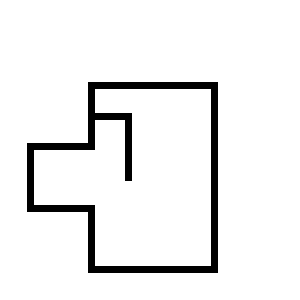

```mathematica
wallA2=Table[{i,-20},{i,-10,10,1}];
wallB2=Table[{-10,i},{i,-20,-10,1}];
wallC2=Table[{i,-10},{i,-20,-10,1}];
wallD2=Table[{-20,i},{i,-10,0,1}];

wallE2=Table[{i,0},{i,-20,-10,1}];
wallF2=Table[{-10,i},{i,0,10,1}];
wallG2=Table[{i,10},{i,-10,10,1}];
wallH2=Table[{10,i},{i,-20,10,1}];

a2=Table[{-4,i},{i,-5,5,1}];
b2=Table[{i,5},{i,-10,-4}];


map2=Join@@{a2,b2,wallA2,wallB2,wallC2,wallD2,wallE2,wallF2,wallG2,wallH2};

Graphics[Rectangle/@map2,ImageSize->300,PlotRange->{{-20,20},{-20,20}}]
```

#### Test 3

```mathematica
RandomInteger[]
```

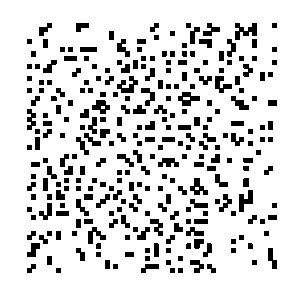

```mathematica
map3=DeleteCases[Table[{RandomInteger[{-30,30}],RandomInteger[{-30,30}]},{i,600}],{0,0}];

Graphics[Rectangle/@map3,ImageSize->300,PlotRange->{{-30,30},{-30,30}}]
```

#### Test 4

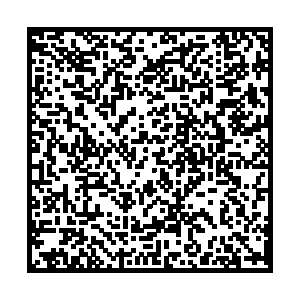

```mathematica
a4=Table[{-30,i},{i,-30,30}];
b4=Table[{30,i},{i,-30,30}];
c4=Table[{i,-30},{i,-30,30}];
d4=Table[{i,30},{i,-30,30}];
borders4=Join@@{a4,b4,c4,d4};
obstacles4=Table[{RandomInteger[{-30,30}],RandomInteger[{-30,30}]},{i,1800}];
map4=DeleteCases[Join[borders4,obstacles4],{0,0}];
Graphics[Rectangle/@map4,ImageSize->300,PlotRange->{{-30,31},{-30,31}}]
```

#### Scan mode

```mathematica
position={0,0};
velocity={1,1}; 

discoveredMap={{0,0}};
walls={{}};
directions={"Forward","Right","Back","Left"};
sensors=updateSensors[position,map4];
pause=1;

nextDirection=RandomChoice[directions];
bin=Databin[Last[Values[controlBin]][[1]]];

status={TimeObject[Now],position,nextDirection,sensors,walls,discoveredMap}
test={};
Print[sensors,nextDirection,position];


Do[
timestampNew=TimeObject[Now];
previousStatus=status;
positionNew=updatePosition[timestampNew,previousStatus,velocity];
sensors=updateSensors[positionNew,map4];

wallsNew=updateWalls2[positionNew,previousStatus,sensors];

mapNew=updateMap[positionNew,timestampNew,previousStatus];

nextDirection=updateDirection2[directions,sensors,previousStatus[[3]]];
status={timestampNew,positionNew,nextDirection,sensors,wallsNew,mapNew};
test=Append[test,status];
Pause[pause];
,{loop,1000}]
```

{17:15:27GMT-4.TimeObject[{17,15,27.3529},TimeZone→-4.],{0,0},Right,{0,0,0,1},{{}},{{0,0}}}

```mathematica
states=test;
```

```mathematica
Manipulate[
Overlay[
{
Graphics[{Green,Rectangle/@states[[frame,6]],Blue,Rectangle[states[[frame,2]]],Style[Rectangle/@DeleteCases[states[[frame,5]],{}],Red]},PlotRange->{{states[[frame,2,1]]-40,states[[frame,2,1]]+40},{states[[frame,2,2]]-40,states[[frame,2,2]]+40}},ImageSize->{300}],

Framed[
Graphics3D[
{
Blue,Cuboid[Join[states[[frame,2]],{0}]],
Green,Cuboid/@Table[Join[states[[frame,6,i]],{-1}],{i,Length[states[[frame,6]]]}],

Style[Cuboid/@Table[If[states[[frame,5,i]]=={},Nothing,Join[DeleteCases[states[[frame,5,i]],{}],{0}]],{i,Length[states[[frame,5]]]}],Red]

},
Boxed->False,PlotRange->{{states[[frame,2,1]]-5,states[[frame,2,1]]+5},{states[[frame,2,2]]-5,states[[frame,2,2]]+5},{0,3}},ImageSize->100,ViewAngle->Pi/16]
]
},
Alignment->{Right,Top}
],{frame,1,Length[states],1}]
```

```mathematica
Export["image.gif",Table[
Overlay[
{
Graphics[{Green,Rectangle/@states[[frame,6]],Blue,Rectangle[states[[frame,2]]],Style[Rectangle/@DeleteCases[states[[frame,5]],{}],Red]},PlotRange->{{states[[frame,2,1]]-40,states[[frame,2,1]]+40},{states[[frame,2,2]]-40,states[[frame,2,2]]+40}},ImageSize->{300}],

Framed[
Graphics3D[
{
Blue,Cuboid[Join[states[[frame,2]],{0}]],
Green,Cuboid/@Table[Join[states[[frame,6,i]],{-1}],{i,Length[states[[frame,6]]]}],

Style[Cuboid/@Table[If[states[[frame,5,i]]=={},Nothing,Join[DeleteCases[states[[frame,5,i]],{}],{0}]],{i,Length[states[[frame,5]]]}],Red]

},
Boxed->False,PlotRange->{{states[[frame,2,1]]-5,states[[frame,2,1]]+5},{states[[frame,2,2]]-5,states[[frame,2,2]]+5},{0,3}},ImageSize->100,ViewAngle->Pi/16]
]
},
Alignment->{Right,Top}
],{frame,1,Length[states],1}]]
```

image.gif

```mathematica
Animate[
Overlay[
{
Graphics[{Green,Rectangle/@states[[frame,6]],Blue,Rectangle[states[[frame,2]]],Style[Rectangle/@DeleteCases[states[[frame,5]],{}],Red]},PlotRange->{{states[[frame,2,1]]-40,states[[frame,2,1]]+40},{states[[frame,2,2]]-40,states[[frame,2,2]]+40}},ImageSize->{300}],

Framed[
Graphics3D[
{
Blue,Cuboid[Join[states[[frame,2]],{0}]],
Green,Cuboid/@Table[Join[states[[frame,6,i]],{-1}],{i,Length[states[[frame,6]]]}],

Style[Cuboid/@Table[If[states[[frame,5,i]]=={},Nothing,Join[DeleteCases[states[[frame,5,i]],{}],{0}]],{i,Length[states[[frame,5]]]}],Red]

},
Boxed->False,PlotRange->{{states[[frame,2,1]]-5,states[[frame,2,1]]+5},{states[[frame,2,2]]-5,states[[frame,2,2]]+5},{0,3}},ImageSize->100,ViewAngle->Pi/16]
]
},
Alignment->{Right,Top}
],{frame,1,Length[states],1},DisplayAllSteps->True]
```

```mathematica
Length[states]
```

```mathematica
Export["image.gif",Table[
Overlay[
{
Graphics[{Green,Rectangle/@states[[frame,6]],Blue,Rectangle[states[[frame,2]]],Style[Rectangle/@DeleteCases[states[[frame,5]],{}],Red]},PlotRange->{{states[[frame,2,1]]-40,states[[frame,2,1]]+40},{states[[frame,2,2]]-40,states[[frame,2,2]]+40}},ImageSize->{300}],

Framed[
Graphics3D[
{
Blue,Cuboid[Join[states[[frame,2]],{0}]],
Green,Cuboid/@Table[Join[states[[frame,6,i]],{-1}],{i,Length[states[[frame,6]]]}],

Style[Cuboid/@Table[If[states[[frame,5,i]]=={},Nothing,Join[DeleteCases[states[[frame,5,i]],{}],{0}]],{i,Length[states[[frame,5]]]}],Red]

},
Boxed->False,PlotRange->{{states[[frame,2,1]]-5,states[[frame,2,1]]+5},{states[[frame,2,2]]-5,states[[frame,2,2]]+5},{0,3}},ImageSize->100,ViewAngle->Pi/16]
]
},
Alignment->{Right,Top}
],{frame,1,Length[states],1}]]
```

## Graphical User Interface (GUI)

A GUI was created in Mathematica to control the robot, allowing it to shift between Scanning and Control modes.

```mathematica
DatabinAdd[Databin["dSFSYX3k"],{"dVQXR0Tx","Scan","Stop","Execute"}]
```

Databin[…]

```mathematica
DatabinAdd[Databin["dSFSYX3k"],{"dVQXR0Tx","Control","Stop","Abort"}]
```

```mathematica
controlBin=Databin["dSFSYX3k"];
(*rBin="dU8AFtnw";*)
rBin="dVQXR0Tx";
showmap=False;
Column[{
Row[
{Button["Clear bin",DatabinRemove[Databin[rBin],1;;Length[Values[Databin[rBin]]]],Appearance->"Palette",FrameMargins->Medium],

Button["Start scanning",DatabinAdd[Databin["dSFSYX3k"],{rBin,"Scan","Stop","Execute"}],Appearance->"Palette",FrameMargins->Medium],

Button["Control mode",DatabinAdd[Databin["dSFSYX3k"],{rBin,"Control","Stop","Execute"}],Appearance->"Palette",FrameMargins->Medium],

Button["Finish",DatabinAdd[Databin["dSFSYX3k"],{rBin,"Control","Stop","Abort"}],Appearance->"Palette",FrameMargins->Medium],

Button["Update states",states=Drop[Values[Databin[rBin]],6],Appearance->"Palette",FrameMargins->Medium],

Button["Toggle map",showmap=Not[showmap],Appearance->"Palette",FrameMargins->Medium]},
Alignment->Center]
,

Dynamic[

If[showmap==True,Manipulate[


Overlay[
{
Graphics[{Green,Rectangle/@states[[frame,6]],Blue,Rectangle[states[[frame,2]]],Style[Rectangle/@DeleteCases[states[[frame,5]],{}],Red]},PlotRange->{{states[[frame,2,1]]-40,states[[frame,2,1]]+40},{states[[frame,2,2]]-40,states[[frame,2,2]]+40}},ImageSize->{300}],

Framed[
Graphics3D[
{
Blue,Cuboid[Join[states[[frame,2]],{0}]],
Green,Cuboid/@Table[Join[states[[frame,6,i]],{-1}],{i,Length[states[[frame,6]]]}],

Style[Cuboid/@Table[If[states[[frame,5,i]]=={},Nothing,Join[DeleteCases[states[[frame,5,i]],{}],{0}]],{i,Length[states[[frame,5]]]}],Red]

},
Boxed->False,PlotRange->{{states[[frame,2,1]]-5,states[[frame,2,1]]+5},{states[[frame,2,2]]-5,states[[frame,2,2]]+5},{0,3}},ImageSize->100,ViewAngle->Pi/16]
]
},
Alignment->{Right,Top}
],{frame,1,Length[states],1}],-Graphics-]]

,
Row[{Spacer[100],Button[-Graphics-,DatabinAdd[Databin["dSFSYX3k"],{rBin,"Control","Forward","Execute"}],Appearance->"Palette"]}],
Row[{Button[-Graphics-,DatabinAdd[Databin["dSFSYX3k"],{rBin,"Control","Left","Execute"}],Appearance->"Palette"],Spacer[125],Button[-Graphics-,DatabinAdd[Databin["dSFSYX3k"],{rBin,"Control","Right","Execute"}],Appearance->"Palette"]}],
Row[{Spacer[100],Button[-Graphics-,DatabinAdd[Databin["dSFSYX3k"],{rBin,"Control","Back","Execute"}],Appearance->"Palette"]}]}]
```

Clear binStart scanningControl modeFinishUpdate statesToggle map

-Graphics-
-Graphics--Graphics-
-Graphics-